```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/Moat-meanfield/MF_DR/spec/gif_data/mu0T1

```mathematica
Re1=Import["./RedataT1mu0.dat"];
Im1=Import["./ImdataT1mu0.dat"];
Re2=Re1;
Im2=Im1;
omega=Table[i,{i,1,701,5}];
ps=Table[i,{i,1,501,5}];
Reall=Flatten[Table[{x=omega[[j]],y=ps[[i]],Re2[[i]][[j]]},{i,1,101},{j,1,141}],1];
infRe=Interpolation[Reall];
spec=-1/π*(Im2-1)/(Re2^2+(Im2-1)^2);
```

```mathematica
cp=ContourPlot[infRe[x,y],{x,1,701},{y,1,501},Contours->{0},(*零点曲线*)ContourShading->False,PlotPoints->50,MaxRecursion->3];
pole=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
pole3D1=({#[[1]],#[[2]],1}&/@pole);
pole3D2=({#[[1]],#[[2]],0}&/@pole);
pole3D=Flatten[{pole3D1,pole3D2},1];
```

```mathematica
omegapole=Transpose[pole][[1]];
pspole=Transpose[pole][[2]];
```

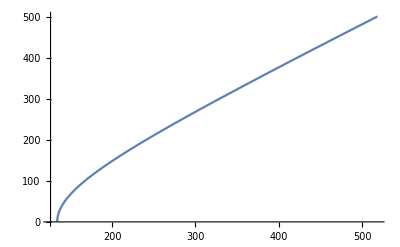

```mathematica
ListLinePlot[Transpose[{omegapole,pspole}]]
```

```mathematica
Dimensions[Re2]
```

{101,141}

```mathematica
ListPlot3D[Reall,PlotRange->{All,All,All}]
```

-Graphics3D-

```mathematica
ListPlot3D[spec,PlotRange->{All,All,(*{0,2 10^-7}*){0,2 10^-7}}]
```

-Graphics3D-

```mathematica
special=Clip[spec,{0,0.0000015}];
```

```mathematica
ListPlot3D[special]
```

-Graphics3D-

```mathematica
(*Export["spec.dat",special]*)
```

spec.dat